## DIRK - Diagonally Implicit Runge–Kutta methods

Francesco Torsello

References
[1] J. C. Butcher, Numerical Methods for Ordinary Differential Equations, John Wiley & Sons, 2008, ISBN: 9780470753750
[2] NASA, Diagonally Implicit Runge-Kutta Methods for Ordinary Differential Equations. A Review. https://ntrs.nasa.gov/archive/nasa/casi.ntrs.nasa.gov/20160005923.pdf
[3] Stål, Josefine, Implementation of Singly Diagonally Implicit Runge-Kutta Methods with Constant Step Sizes, Bachelor’s Theses in Mathematical Sciences, 2015, ISSN: 1654-6229, http://lup.lub.lu.se/student-papers/record/7851608

[4] A. Kværnø, S.P. Nørsett, B. Owren, Runge-Kutta research in Trondheim, Applied Numerical Mathematics, Volume 22, Issues 1–3, 1996, pp. 263-277, ISSN 0168-9274, https://doi.org/10.1016/S0168-9274(96)00037-2

[5] Kværnø, Singly Diagonally Implicit Runge–Kutta Methods with an Explicit First Stage, A.BIT Numerical Mathematics (2004) 44 : 489. https : // doi.org/10.1023/B : BITN .0000046811 .70614 .38

Useful links
[6] https://en.wikipedia.org/wiki/List_of_Runge % E2 %80 %93 Kutta_methods

### The differential equation and its exact solution

Here we define the differential equation to integrate and find its exact solution.

```mathematica
Clear[f];
f[t_,r_,y_]:=y^2/((1+y)r) ⅇ^(-t^2);
```

```mathematica
DSolve[{D[y[t,r],t]==y[t,r]^2/((1+y[t,r])r) ⅇ^(-t^2),y[0,r]==2.43763},{y[t,r]},{t,r}]⟦1,1,2⟧//Quiet
```

1/ProductLog[ⅇ^(-0.480792-(√π Erf[t])/(2 r))]

```mathematica
Clear[ExactSolution];
ExactSolution[t_,r_]:=1/ProductLog[ⅇ^(-0.4807917247196075-(√π Erf[t])/(2 r))]
```

### The chosen DIRK method

We take the following two excerpts from [4],

-Graphics-

-Graphics-

#### ESDIRK 3/2 with s=4 stages, L-stable, not embedded

This method is taken from [5, p.497].

```mathematica
s=4;
```

```mathematica
c={{0},{2γ},{1},{1}};
```

```mathematica
A={
{0,0,0,0},
{γ,γ,0,0},
{(-4 γ^2+6γ-1)/(4γ),(-2γ+1)/(4γ),γ,0},
{(6γ-1)/(12γ),-1/(12(2γ-1)γ),(-6 γ^2+6γ-1)/(6γ-3),γ}
};
```

```mathematica
ESDIRK32=MapThread[Join,{c,A}];
```

```mathematica
ESDIRK32$BT=Grid[ESDIRK32,Dividers->{{False,True},False}]
```

0 | 0 | 0 | 0 | 0
2 γ | γ | γ | 0 | 0
1 | (-1+6 γ-4 γ^2)/(4 γ) | (1-2 γ)/(4 γ) | γ | 0
1 | (-1+6 γ)/(12 γ) | -1/(12 γ (-1+2 γ)) | (-1+6 γ-6 γ^2)/(-3+6 γ) | γ

The parameter γ is set by solving the condition for L-stability for it.

```mathematica
LStability[s_]:=Γ^(s-1)LaguerreL[s-1,1/Γ]==0
```

```mathematica
LStability[s]//Simplify
```

9 Γ+6 Γ^3==1+18 Γ^2

```mathematica
Clear[SolveCubicEquation];
SolveCubicEquation[a_,b_,c_,d_]:=
Module[{Δ0,Δ1,Δ,C,x},
Δ0=b^2-3a c;
Δ1=2 b^3-9a b c +27 a^2 d;
C=CubeRoot[(Δ1+Sqrt[Δ1^2-4 Δ0^3])/2];
x=-1/(3a)(b+C+Δ0/C)//Simplify;
Return[x];
]
```

```mathematica
SolveCubicEquation[6,-18,9,-1]
```

CubeRoot::preal: The parameter 1/2 (-3888+972 ⅈ √2) should be real valued.

1-9/(486 ⅈ (4 ⅈ+√2))^(1/3)-1/18 (486 ⅈ (4 ⅈ+√2))^(1/3)

```mathematica
NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]
```

{{Γ→0.158983899988676546782594777575},{Γ→0.435866521508458999416019451194},{Γ→2.40514957850286445380138577123}}

```mathematica
γ=NSolve[LStability[4],Γ,Reals,WorkingPrecision->30]⟦2,1,2⟧;
```

```mathematica
ESDIRK32$BT
```

0 | 0 | 0 | 0 | 0
0.871733043016917998832038902387 | 0.435866521508458999416019451194 | 0.435866521508458999416019451194 | 0 | 0
1 | 0.49056338842178057062846795847 | 0.07357009006976042995551259034 | 0.435866521508458999416019451194 | 0
1 | 0.30880996997674652334816246989 | 1.4905633884217805706284679585 | -1.23523987990698609339264988 | 0.435866521508458999416019451194

### Solving the implicit system

-Graphics-

```mathematica
m=1;
r0=1;
t0=0;
h=0.01;
t[0]=t0;
y[0]=2.43763;
𝕀[1]=1;
𝕀[m_]:=IdentityMatrix[m];
```

Y[n,i][k] means value of the variable Y at time step n, stage i and iteration k.

```mathematica
Clear[step$n$stage$i];
step$n$stage$i[n_,i_]:=y[n]+h Sum[A⟦i,j⟧f2[t[n]+c⟦j,1⟧h,r0, Y[n,j]],{j,1,s}]//Simplify
```

```mathematica
f2[t[1],r0,step$n$stage$i[1,1]]
```

(ⅇ^(-t[1]^2) (0.+y[1])^2)/(1.+y[1])

```mathematica
Clear[J];
J[n_]:=D[f2[t[np],r0,step$n$stage$i[np,1]],y[np]]/.{np->n}
```

```mathematica
J[0]
```

0.915378

```mathematica
ℕ[n_,i_]:=𝕀[m]-h A⟦i,i⟧J[n]
```

```mathematica
ℕ[0,1]
```

1.

Here we are setting the initial data.

```mathematica
Y[0,1][0]=y[0]+0.05436h;
```

```mathematica
0.05436h
```

0.002718

The following functions are at a fixed r.

```mathematica
tol=10^-4;
```

```mathematica
Clear[computeStage];
computeStage[n_,i_,tolerance_]:=Module[{dis,k},
dis=10^3;
k=0;
While[Abs[dis]>tolerance,
dis=Solve[
	ℕ[n,i]x==-(Y[n,i][k]-y[n])+h Sum[A⟦i,j⟧f2[t[n]+c⟦j,1⟧h,r0, Y[n,j][n$iteration[j]]],{j,1,i-1}]
			  +h  Sum[A⟦i,s⟧f2[t[n]+c⟦s,1⟧h,r0, Y[n,s][k]],{j,i,s}],
x]⟦1,1,2⟧;
Y[n,i][k+1]=Y[n,i][k]+dis;
++k;
];
n$iteration[i]=k-1;
Y[n,i+1][0]=Y[n,i][k-1];
]
```

```mathematica
Clear[computeStep];
computeStep[n_,tol_]:=Module[{σ},
For[σ=1,σ≤s,σ++,
computeStage[n,σ,tol];
];
y[n+1]=Y[n,σ][0];
Y[n+1,1][0]=Y[n,σ][0];
]
```

```mathematica
computeStep[0,tol]
```

```mathematica
y[1]
```

2.52554

```mathematica
computeStep[1,tol]
```

```mathematica
y[2]
```

2.6171

```mathematica
Clear[integrate];
integrate[t0_,t1_,tol_]:=Module[{m},
m=0;
t[0]=t0;
Monitor[
While[t[m]≤t1,
computeStep[m,tol];
t[m+1]=t[m]+h;
++m;
],
t[m]];
m$size=m;
Print["Integration performed from t="<>ToString[t0]<>" to t="<>ToString[t1]<>" in m="<>ToString[m$size]<>" steps."];
]
```

```mathematica
integrate[0,10,tol]
```

Integration performed from t=0 to t=10 in m=1001 steps.

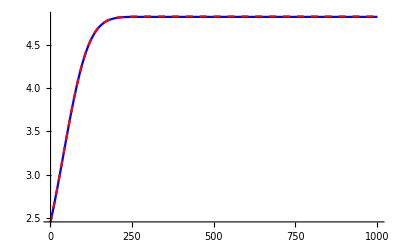

```mathematica
DiscretePlot[
{y[n],ExactSolution[t[n],r0]},
{n,1,m$size},
PlotRange->Full,
PlotStyle->{Blue,{Red,Dashed}},
Filling->None,
Joined->True
]
```